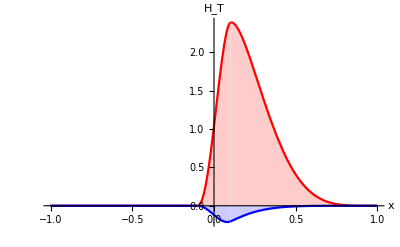

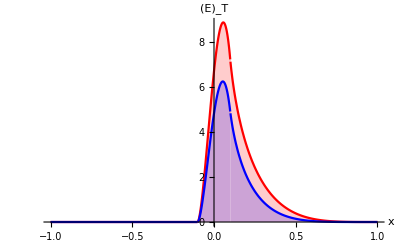

```mathematica
Plot[{HTu[x,0.1,-0.0],HTd[x,0.1,-0.0]},{x,-1.0,1.0},PlotRange->All,PlotStyle->{Red,Blue},AxesLabel->{"x","H_T"},Filling->Axis]

Plot[{EbarTu[x,0.1,-0.0],EbarTd[x,0.1,-0.0]},{x,-1.0,1.0},PlotRange->All,PlotStyle->{Red,Blue},AxesLabel->{"x","(Ē)_T"},Filling->Axis]
```

```mathematica
ksi=0.01;
Integrate[HTu[x,ksi,0.],{x,0,1}]
Integrate[HTd[x,ksi,0.],{x,0,1}]
Integrate[EbarTu[x,ksi,0.],{x,0,1}]
Integrate[EbarTd[x,ksi,0.],{x,0,1}]
```